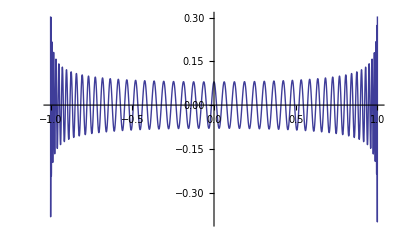

```mathematica
Plot[LegendreP[100,x],{x,-1,1}]
```

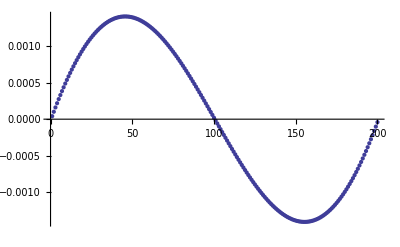

```mathematica
n=200;
tb1=Sort[x/.NSolve[LegendreP[n,x]==0,x,Reals,WorkingPrecision->1000]];
tb2=Sort[N[Table[Cos[π (2k-1)/(2n)],{k,n}]]];
ListPlot[tb1-tb2]
```